## Welcome to Mathematica!

For those who already have experience with Mathematica, this lesson will seem simple, but there are a few things that courses such as Chem 5 do not show you. So you may want to look at the last section (section 9).

NOTE: If you are not using a Mac, the ctrl key on your keyboard can be replaced in every instance that I mention pressing the Command key. Yes, this notebook was written using a Mac.

### 1) Using Plain Text

#### 1.1) Adding Comments

To start, we can add plain text to any notebook in Mathematica by going to the Writing Assistant under Palettes at the top of your screen and clicking on Text cell. The writing assistant will stay on the right side of your screen for the rest of the session until you decide to close it.

Every new cell created is defaulted to only letting you type commands and can’t be used to display general text. To convert a new cell to allow plain text, you can use the shortcut Command-7 instead of having to go to the writing assistant every time. When you want to use a new cell, you can click on the empty space below your current cell or press on the down arrow key once.

To add a title to your notebook, you can go to Title cells in the writing assistant or press Command-4 or Command-5 depending on whether you want define a section or a subsection. The “Welcome to Mathematica” at the beginning of this notebook was made using Command-4, while the “Adding text” was made using Command-5.

#### 1.2) Adding Equations

If you want to write out equations or add math symbols in plain text, you can use the Basic Math Asssitant that’s also under Palettes and look through the Typesetting section. You can use this to write out equations that look like this: 

∫_(-∞)^∞ e^(-x^2)dx = 0
∮ dS = 0 ⟹ 0 ≥ δq/T
PbSO_(4(s))⟶ (Pb_(aq))^(2+)+(SO_(4(aq)))^(2-)

To make font larger and smaller, press Command-(+) or Command-(-).

With that, you can now write out any homework assignment for any class on a Mathematica notebook!

### 2) Basic arithmetic

When you want Mathematica to evalue a cell, you can press Shift-Enter. Try it with this input below:

```mathematica
2+2
```

4

If you want to delete an entire cell, you can click on the bracket to the right of the cell and press delete on your keyboard. If you delete something that you didn’t want to delete, use Command-Z to undo the mistake.

( + ) and ( - ) indicate addition and subtraction, respectively, but the asterisk ( * ) and ( / ) indicate multiplication and division, respectively. If you want to define exponentials, you use ( ^ )  when creating the exponent. You can also use the Basic Math Assistant to type out your equations.

```mathematica
4^4
```

256

Mathematica also follows the standard order of operations, which is the PEMDAS logic that you learned a long time ago in math. This means that in any expression you define, Mathematica will evaluate (from left to right) anything in parantheses first, then exponents (powers or roots), then multiplication and division, and then addition and subtraction.

```mathematica
4-5/5+2*3
```

9

In this example, 5 / 5 and 2 * 3 were evaluated first, leaving 4 - 1 + 6 . Since Mathematica evaluates an expression from left to right, it gave 3 + 6 rather than 4 - 7.

### 3) Commonly used numbers

Mathematica has constants that are built in and never have to be defined such as π, e, and the imaginary number i.

```mathematica
Pi
```

π

```mathematica
E
```

ⅇ

```mathematica
I
```

ⅈ

```mathematica
I^2
```

-1

### 4) Variables

You can define a variable by simply using any letter of your choice followed by an equal sign and whatever numerical value you want to assign to the variable.

```mathematica
a=1
```

1

To tell if your variable already has something assigned to it or not, the variable will be blue if nothing has been assigned to it and the variable will be black if there is something assigned to it. 
To make a variable free, use the Clear function. Mathematica won’t give any output when you use Clear and will simply turn the variable blue again.

```mathematica
Clear[a]
```

If you’re assigning multiple variables and you don’t want to display the output, add a semicolon ( ; ) after any assignment.

```mathematica
k=2;
```

There are a few things to keep in mind when your notebook contains a lot of variables. Variable names are case sensitive, so “ A “ and  
“ a “ can be defined as different variables. Although, it’s good practice to stick to one convention (i.e. making all variable names upper-case or making all variable names lower-case). You also cannot use the dash symbol ( - ) or the underscore ( _ )  when defining variables like you can in other programming languages. Mathematica will give you an error message if you try to use dashes or underscores in your variable names.

### 5) Functions

Mathematica has hundreds of thousands of built in functions/commands (not to be confused with functions in math), but there are only a few that will be useful to memorize. Generally, the argument of a function in Mathematica is enclosed in square brackets and the name of the function is also case sensitive. The names of Mathematica’s built in functions typicallly start with a capital letter followed by lowercase letter(s).

```mathematica
Sqrt[2]
```

√2

Mathemtica by default uses the natural logarithm, (i.e. a logarithm with base e).

```mathematica
Log[E]
```

1

If you want to compute the logarithm with a different base, you can use Log[b, c] , where b is the base and c is the expression.

```mathematica
Log[10,1000]
```

3

```mathematica
Sin[Pi]
```

0

```mathematica
Cos[Pi]
```

-1

```mathematica
Abs[-5]
```

5

Mathematica will usually get lazy and give you outputs in terms of fractions, whenever it can. The function N gives the closest numerical approximation of a given fraction or expression.

```mathematica
4/5
```

4/5

```mathematica
N[4/5]
```

0.8

This can be very useful when you want a value as a decimal and not some complicated fraction because the N function forces Mathematica to give the approximate value.

```mathematica
E^(1-999)
```

1/ⅇ^998

```mathematica
N[E^(1-999)]
```

3.75065450499×10^-434

If you want an output with n-digit precision, you can follow the expression in the argument with a comma and the number of digits you want. So if you wanted 30 digits after the decimal point, you’d do the following:

```mathematica
N[E^(1-999),30]
```

3.75065450498591130695835115856×10^-434

To define your own mathematical functions, you need to write out the name of your function (upper or lower case), and then have the variable followed by an underscore as an argument enclosed in brackets. Then use the colon and equal sign to tell Mathematica that you are defining a function.

```mathematica
f[x_]:=x^2
```

```mathematica
f[2]
```

4

```mathematica
f[Pi]
```

π^2

And you can clear the function by clearing the name of the function. When a function is not defined, the name of the function will appear as blue. Once it is defined, the name will appear as black. You can see for yourself by evaluating the bottom cell if you defined the function before.

```mathematica
Clear[f]
```

Defining functions with multiple variables can be done in a similar way. Just add your variables, making sure they are separated by commas, and don’t forget to add the underscore when defining the function.

```mathematica
g[x_,y_]:=x*y^2
```

```mathematica
g[x,y]
```

x y^2

```mathematica
g[2,3]
```

18

```mathematica
g[Pi,y]
```

π y^2

### 6) Graphing

#### 6.1) Single Variable Functions

For this class, it will be very useful to know how to make plots of various things. Mathematica can make a plot of various functions by just using the Plot function. When plotting, you need to specify the function you want to plot and a minimum and maximum value for Mathemtica to display along the horizontal axis. Mathematica, by convention, will consider the input variable of your function to be the horizontal axis and the output variable to be the vertical axis, just like in all of your math classes.



```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

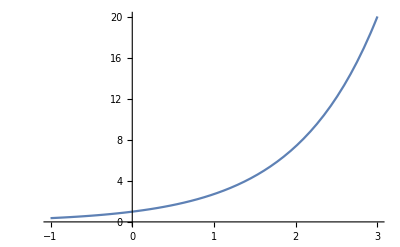

```mathematica
Plot[E^x,{x,-1,3}]
```

#### 6.2) Example

We can also plot functions that we have defined. Take for example, the ideal gas law! By defining the pressure as a function of the temperature (holding the volume constant), we can take any set of temperatures at various conditions and see how the pressure of the gas changes.

For example, let’s define 3 containers that have the same ideal gas. To make it simple, we’ll define containers a, b, and c where:
container a is 10 liters and has 1 mole of gas; container b is 4 liters and has 4 moles of gas; container c is 1 liter and has 1 mole of gas. Since the ideal gas law can be written as P(T) = nRT/V, we can make our plots of P_a, P_b, and P_c by defining the moles of each container as n_a, n_b, and n_c and the volumes as V_a, V_b, V_c.

```mathematica
na=1;
nb=4;
nc=8;
va=10;
vb=10;
vc=10;
r=0.082056;
pa[t_]:=(na*r*t)/va
pb[t_]:=(nb*r*t)/vb
pc[t_]:=(nc*r*t)/vc
```

If you want to create plots with axes labels and plot titles, simply use the commands AxesLabel and PlotLabel. Both commands are used by adding a right arrow, followed by the names of your axes in quotes, separated by commas, inside curly brackets. The ordering of the names is such that the first name is for the horizontal axis and the second name is for the vertical axis.

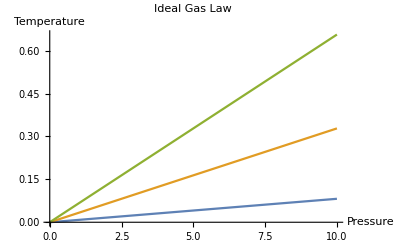

```mathematica
Plot[{pa[t],pb[t],pc[t]},{t,0,10},AxesLabel->{"Pressure","Temperature"},PlotLabel->"Ideal Gas Law"]
```

#### 6.3) Multi-Variable Functions

If you want to graph functions of 2 variables, you use the Plot3D function in a very similar way that you used the Plot function. Once the graph is made, you can click and drag the graph to move it around and get a better angle of the surface.

```mathematica
f[x_,y_]:=x^2+y^2;
Plot3D[f[x,y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

### 7) Differentiation

#### 7.1) Functions of One Variable

Now that you know the basics of how to play around with variables and functions, it will be very useful to know how to compute derivatives and integrals since P-chem is expecting you to already know how to do them. But it’s always nice to have a program that you can use to check your work.

Starting with defining a function h(x), there are two ways we can compute its derivative.

```mathematica
h[x_]:=3*x^5
```

The first way is to use the function D, which requires the argument to be the function whose derivative is being computed and the variable 
its taken with respect to, separated by a comma.

```mathematica
D[h[x],x]
```

15 x^4

The second way is to type the function with an apostrophe ( ‘ ) that can be treated like the “prime”. For example,  “h prime” is the first derivative, “h double prime” is the second derivative, etc.

```mathematica
h'[x]
```

15 x^4

```mathematica
h''[x]
```

60 x^3

```mathematica
h'''[x]
```

180 x^2

Using the apostrophe does not work with functions that have more than one variable, so it is best to stick with the function D. To compute 
multiple derivatives with D, type  D[ h[x] , {x,n} ] , where n is the n-th derivative you want to compute.

```mathematica
D[h[x],{x,3}]
```

180 x^2

The evaluated cell above is the same as saying (∂^3 g(x))/(∂x^3) = 180 x^2.

#### 7.2) Functions of Multiple Variables

For functions with multiple variables, you can take partial derivatives by typing  D[ f[ x, y, z, ...], x , y, z, ...]  where Mathematica 
differentiates your function with respect to the leftmost vairable in the argument and continues to the rightmost variable.

```mathematica
a[x_,y_]:=2 y^2+x*y^2;
a[x,y]
```

2 y^2+x y^2

```mathematica
D[a[x,y],x,y]
```

2 y

So Mathematica differentiated the function with respect to x first and then with respect to y.

### 8) Integration

#### 8.1) Functions of One Variable

As for integrals, there is only one way to compute them. An indefinite integral (an integral without limits) can be computed by
typing Integrate[ g[x] , x] . We can use h(x) = 3 x^5 from before.

```mathematica
Integrate[h[x],x]
```

x^6/2

A definite integral (an integral with limits) can be computed by typing Integrate[ g[x] , {x, a, b} ]  where a is the lower limit and 
b is the upper limit.

```mathematica
Integrate[h[x],{x,-1,2}]
```

63/2

The above cell says that ∫_-1^2 3 x^5 dx = 63/2.

#### 8.2) Functions of Multiple Variables

For functions with multiple variables, take 3 variables for example, you can type  [ f[x] , {x , a_1, b_1} , {y , a_2 , b_2} , {z, a_3, b_3} ]  which computes ∫_a_1^b_1 ∫_a_2^b_2 ∫_a_3^b_3 f(x)dz dy dx . To compute the integral without limits of integration, use the integrate function without adding limits nor curly braces in the argument [ f[x] , x , y , z ] .

#### 8.3) Numerical Integration

If an integral cannot be evaluated exactly, you can find a numerical approximation by using NIntegrate. For example, if you try to evaluate ∫_0^∞ e^(-x^3)dx , Mathematica will output ...

```mathematica
Integrate[Exp[-x^3],{x,0,Infinity}]
```

Gamma[4/3]

So we just add the N in front of the whole thing, and we get a numerical approximation.

```mathematica
NIntegrate[Exp[-x^3],{x,0,Infinity}]
```

0.89298

For extra information, Mathemtica uses adaptive quadrature as the default method for integrating a function numerically.

And that’s all the basics of Mathematica that you need to know to get through this course! As you continue in the P-chem series, you’ll see that you can use everything you learned in this notebook in any of those courses as well. You can even use what you learned here for any other course you’ll have to take! Good luck!

### 9) Extra features

As I said before, courses such as Chem 5 do not discuss a few shortcuts and features that are built into Mathematica but are useful to know.

#### 9.1) Symbols

Many times, equations come with variables and constants such as  θ , ρ , and π. One way to input these symbols into your cell without having to go through the “Palettes” section each time is to use the esc key on your keyboard. If you hit the escape key once and type the first letter of any symbol’s name, you’ll get the option to choose what symbol you want to add.

You can even use symbols such as theta, kappa, and epsilon as variables like you would with x, y, and z. Just remember to check for the blue and black coloring of the variable.

```mathematica
θ=30
```

30

```mathematica
Clear[θ]
```

A very useful tip is that if you want to clear every variable in a notebook at once, you can type and evaluate the following cell:

```mathematica
ClearAll["Global`*"]
```

#### 9.2) Typing

If you need to add a superscript to something, type control-6 immediately after anything you want to add a subscript to. For subscripts, type control-(dash).

If you want to type a fraction, type control-(forward slash).

If you want to type a square root, type control-2.

For the less than sign, type esc-(<)-(=)-esc. For the greater than sign, type esc-(>)-(=)-esc.

Shortcuts that some people may find intuitive like bold lettering (command-b), italics (command-i), undo (command-z), copy (command-c), and paste (command-v) all work the same in Mathematica.

If you want to make notebooks look pretier, like I failed to do, highlight any text that you want to change the color of and go through the Format section on top of the page. If you want to add a frame over a cell, like one that contains the answer to a question, you can click on the blue frame under Cell Properties in the Writing Assistant.

#### 9.3) Evaluations

If you want to evaluate every cell in a notebook all at once, just click on Evaluate Notebook under Evaluation at the top of the page.

If a compuation is taking too long, you can just press command-(.) to stop the evaluation. You can also click on Abort Evaluation in the Evaluation section on top of the page. Try it for yourself! Evaluate the cell below and Mathematica will print every prime number starting from 1 to 10,000 and it will pause for 0.5 seconds between printing. I have no idea how long that will take.

```mathematica
Do[Print[Prime[n]];Pause[0.5],{n,1,10000}]
```